```mathematica
Exit[]
```

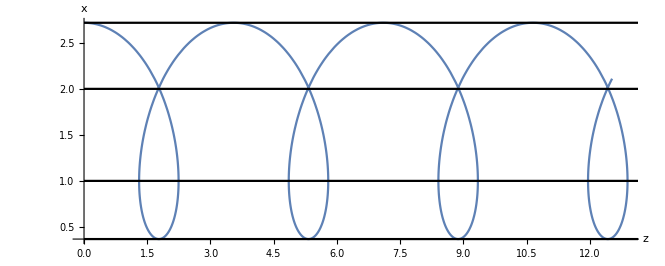

```mathematica
(*charge motion in magnetic field*)
s=NDSolve[{x1'[t]==x4[t],x2'[t]==x5[t],x3'[t]==x6[t],
x4'[t]==(-x1[t] x6[t])/(x1[t]^2+x2[t]^2),x5'[t]==(-x2[t]x6[t])/(x1[t]^2+x2[t]^2),x6'[t]==(x1[t]*x4[t]+x2[t]*x5[t])/(x1[t]^2+x2[t]^2),

x1[0]==E,x2[0]==0,x3[0]==0,x4[0]==0,x5[0]==0,x6[0]==1},{x1[t],x2[t],x3[t]},{t,0,30}];
(*ParametricPlot3D[{x1[t],x2[t],x3[t]}/.s,{t,0,30},PlotRange->Automatic]*)
Show[ParametricPlot[{x3[t],Sqrt[x1[t]^2+x2[t]^2]}/.s,{t,0,30},PlotRange->Automatic,AxesLabel-> {"z","x"}],Plot[{E,1/E,2,1},{t,0,30},PlotStyle->Black]]
```

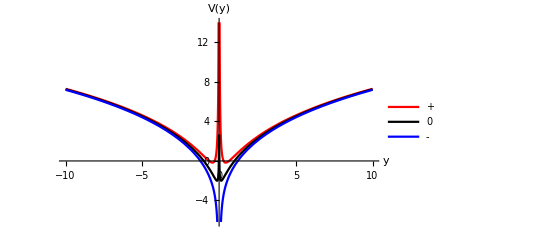

```mathematica
(*effective potential in non-relativistic QM with spin*)
P=2;
Plot[{1/2(Log[Abs[x]])^2+P*Log[Abs[x]]+1/(2Abs[x]),1/2(Log[Abs[x]])^2+P*Log[Abs[x]],1/2(Log[Abs[x]])^2+P*Log[Abs[x]]-1/(2Abs[x])},{x,-10,10},AxesLabel-> {"y","V(y)"},PlotLegends->{"+","0","-"},PlotStyle->{Red,Black,Blue}]
```

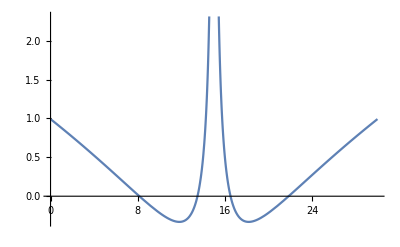

```mathematica
(*potential*)
P=-1;
V[x_]=1/2(Log[Abs[x-a/2]])^2+P*Log[Abs[x-a/2]]+1/(2Abs[x-a/2]);
Plot[V[x],{x,0,a}]
```

```mathematica
(*eigenvalue, state, Wigner distribution*)
```

```mathematica
nmax=100;(*basis set size*)
a=30;(*computational box size*)
ϕ[n_,x_]=√(2/a)Sin[(n π x)/a];
Δ=a/(nmax+1);
xgrid=Range[1,nmax]*Δ;
TM=SparseArray[Band[{1,1}]->Range[1,nmax]^2*π^2/(2 a^2)];
TP=FourierDST[TM,1];
Vgrid=V/@xgrid;
VP=SparseArray[Band[{1,1}]->Vgrid];
HP=TP+VP;
```

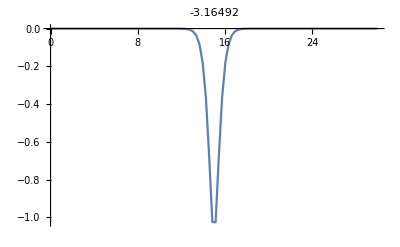

```mathematica
gsP=-Eigensystem[-N[HP],1,Method->{"Arnoldi","Criteria"->"RealPart",MaxIterations->10^6}];
γ=Join[{{0,0}},Transpose[{xgrid,gsP⟦2,1⟧/√Δ}],{{a,0}}];
P1=ListLinePlot[γ,PlotLabel->gsP⟦1,1⟧,PlotRange->All]
```

```mathematica
WignerDistribution[v_?VectorQ]:=With[{nmax=Length[v]},
Function[κ,Evaluate[
Sinc[κ/(nmax+1)]/π×Table[Sum[v⟦j-m⟧Conjugate[v⟦j+m⟧]Exp[(2ⅈ κ m)/(nmax+1)],{m,-Min[j-1,nmax-j],Min[j-1,nmax-j]}]//Re//ComplexExpand,{j,0,nmax+1}]]]]
```

```mathematica
WignerDistributionPlot[v_?VectorQ,{xmin_?NumericQ,xmax_?NumericQ}/;xmax>xmin]:=Module[{nmax,qmax,w,W},
(* number of grid points *)
nmax=Length[v];
(* calculate the Wigner distribution *)
w=WignerDistribution[v];
(* evaluate it on the natural dimensionless momentum grid *)
qmax=Floor[nmax/2];
W=Table[w[q π],{q,-qmax,qmax}];
(* make a plot *)
ArrayPlot[W,FrameTicks->Automatic,DataRange->{{xmin,xmax},(qmax π)/(xmax-xmin){-1,1}},PlotRange->{{xmin,xmax},(qmax π)/(xmax-xmin){-1,1}},AspectRatio->1/GoldenRatio,ColorFunctionScaling->False,ColorFunction->(Blend[{Blue,White,Red},(π#+1)/2]&)]]
```

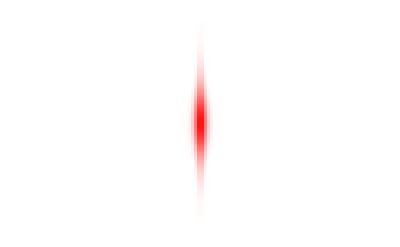

```mathematica
WignerDistributionPlot[gsP⟦2,1⟧,{0,a}]
```

```mathematica
(*wave packet propagation*)
nmax=200;
a=30;
Δ=a/(nmax+1);
xgrid=Range[nmax]*Δ;
Vgrid=V/@xgrid;
propApprox[Δt_?NumericQ,M_Integer/;M≥1,v0_/;VectorQ[v0,NumericQ]]:=Module[{λ,Ke,Pe2,propKin,propPot2,prop},
λ=-I*N[Δt/M];
Ke=Exp[λ*Range[nmax]^2*π^2/(2 a^2)];
propKin[v_]:=FourierDST[Ke*FourierDST[v,1],1];
Pe2=Exp[λ/2*Vgrid];
propPot2[v_]:=Pe2*v;
prop[v_]:=propPot2[propKin[propPot2[v]]];
{Range[0,M]/M Δt,NestList[prop,v0,M]}ᵀ]
```

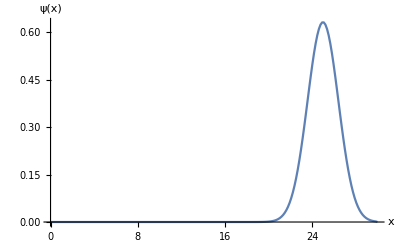

-Graphics-

```mathematica
(*initial wave packet*)
x0=25; 
σ=1;
vv=Normalize[N[ⅇ^(-((xgrid-x0)/(2σ))^2)]];
ListLinePlot[Join[{{0,0}},{xgrid,vv/(√Δ)}ᵀ,{{a,0}}],PlotRange->All,AxesLabel->{"x","ψ(x)"}]
With[{Δt=50,M=1000},
ρ=ArrayPad[Abs[propApprox[Δt,M,vv]⟦All,2⟧]^2/Δ,{{0,0},{1,1}}];
Pq=ArrayPlot[Reverse[Transpose[ρ]],DataRange->{{0,Δt},{0,a}},ColorFunction->(Blend[{Black,Orange},#]&)];
Show[Pq,AspectRatio->1/2,FrameLabel->{t,x},FrameTicks->Automatic,ImageSize-> Large]]
```

```mathematica
{PauliMatrix[1]//MatrixForm,PauliMatrix[2]//MatrixForm,PauliMatrix[3]//MatrixForm}
```

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

```mathematica
gamma0={{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}};
gamma1={{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}};
gamma2={{0,0,0,-I},{0,0,I,0},{0,I,0,0},{-I,0,0,0}};
gamma3={{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}};
```